```mathematica
f[x_]:=1./(1+25*x^2)
a=-1.;
b=1.;
n=4.;
xList = a+1/n*#*(b-a)&/@Range[0,n]
fList = f[xList]
xList2 = {-1+#,-#,#,1-#}&@(1/n)
```

{-1.,-0.5,0.,0.5,1.}

{0.0384615,0.137931,1.,0.137931,0.0384615}

{-0.75,-0.25,0.25,0.75}

```mathematica
w[x_]:=Times@@((x-#)&/@xList)
w[x_,k_]:=Times@@((x-#)&/@Drop[xList,{k}])
```

## Лагранж

```mathematica
lagrange =MapIndexed[ w[x,First@#2]/w[#1,First@#2]&,xList].fList;
Expand@%
```

1.-4.27719 x^2+3.31565 x^4

```mathematica
lagranges={};
(n=#;xList = a+1/n*#*(b-a)&/@Range[0,n];fList=f[xList];AppendTo[lagranges,MapIndexed[ w[x,First@#2]/w[#1,First@#2]&,xList].fList])&/@{4,10,20,40};
```

## Схема Эйткена

```mathematica
ClearAll[Eitken];Eitken[func_,x_,n_]:=Block[{res},
res = {1/(xList[[#+2]]-xList[[#+1]])*
(func[xList[[#+1]]]*(xList[[#+2]]-x)-func[xList[[#+2]]]*(xList[[#+1]]-x))&/@Range[0,n-1]};
For[i=1,i<n,i++,AppendTo[res,(Last[res][[#+1]]*(xList[[#+2+i]]-x)-Last[res][[#+2]]*(xList[[#+1]]-x))/(xList[[#+2+i]]-xList[[#+1]])&/@Range[0,n-1-i]]];
Last[res][[1]]]
```

```mathematica
n=40;xList = a+1/n*#*(b-a)&/@Range[0,n];fList=f[xList];
```

```mathematica
(*eitkens = (n=#;xList = a+1/n*#*(b-a)&/@Range[0,n];fList=f[xList];Eitken[f,x,#])&/@{4,10,20,40};*)
```

## Сплайны

```mathematica
n=4;xList = a+1/n*#*(b-a)&/@Range[0,n];fList=f[xList];
```

```mathematica
fList
```

{0.0384615,0.137931,1.,0.137931,0.0384615}

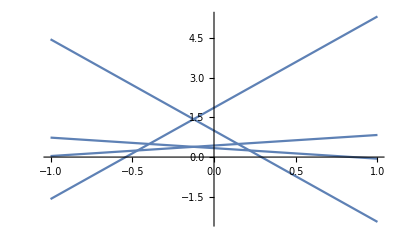

```mathematica
Plot[Expand@Most@fList+n*ListConvolve[{1,-1},fList]*(x-Most@xList),{x,-1,1}]
```

```mathematica
ClearAll[spline];spline[f_,x_,n_]:=Piecewise[MapThread[{#1,#2}&,{Most@fList+ListConvolve[{1,-1},fList]/ListConvolve[{1,-1},xList]*(x-Most@xList),xList[[#]]<=x<xList[[#+1]]&/@Range[1,n]}]]
```

```mathematica
splines = (n=#;xList = a+1/n*#*(b-a)&/@Range[0,n];fList=f[xList];spline[f,x,#])&/@{4,10,20,40};
```

## Сравнение

```mathematica
xLists2 = (n=#;xList2 = {a+#,-#,#,b-#}&@(1/n))&/@N@{4,10,20,40}
```

{{-0.75,-0.25,0.25,0.75},{-0.9,-0.1,0.1,0.9},{-0.95,-0.05,0.05,0.95},{-0.975,-0.025,0.025,0.975}}

```mathematica
MapThread[(#1/.x->#)&/@#2&,{lagranges,xLists2}]
```

{{-0.75,-0.25,0.25,0.75},{-0.9,-0.1,0.1,0.9},{-0.95,-0.05,0.05,0.95},{-0.975,-0.025,0.025,0.975}}

```mathematica
answer = Table[f/@xLists2[[i]],{i,1,4}]
```

{{0.06639,0.390244,0.390244,0.06639},{0.0470588,0.8,0.8,0.0470588},{0.0424403,0.941176,0.941176,0.0424403},{0.0403785,0.984615,0.984615,0.0403785}}

```mathematica
Abs[answer-Table[(lagranges[[i]]/.x->#)&/@xLists2[[i]],{i,1,4}]]
```

{{0.423216,0.355384,0.355384,0.423216},{1.53166,0.0434074,0.0434074,1.53166},{39.9949,0.00131391,0.00131391,39.9949},{57409.2,1.88701×10^-6,1.88701×10^-6,57409.2}}

```mathematica
ns={4,10,20,40};
Abs[answer-((n=ns[[#]];Eitken[f,#,n]&/@xLists2[[#]])&/@Range[4])]
```

{{0.0000143761,0.104822,0.780597,3.5506},{1.38778×10^-17,0.0898636,2.32609,367.503},{6.93889×10^-18,4.44089×10^-16,0.0406948,9.17807×10^8},{57409.2,1.88701×10^-6,1.88701×10^-6,57409.2}}

```mathematica
Abs[answer-Table[(splines[[i]]/.x->#)&/@xLists2[[i]],{i,1,4}]]
```

{{0.0218062,0.178722,0.178722,0.0218062},{0.00158371,0.05,0.05,0.00158371},{0.000319863,0.0411765,0.0411765,0.000319863},{0.0000723795,0.0140271,0.0140271,0.0000723795}}

```mathematica
Eitken[f,#,40]&/@xList2
```

{-57409.2,0.984617,0.984617,-57409.2}

```mathematica
(Eitken[f,x,40]/.x->#)&/@xList2
```

$Aborted